800 MS/s sample rate
200 MHz carrier
(-1 to 1, dBm)

```mathematica
responseData={{1,0.52},{0.1,-19.52},{0.5,-5.7},{0.8,-1.52},{0.9,-0.48},{0.3,-10.15},{0.6,-4.13},{0.7,-2.76},{0.4,-7.65},{0.2,-13.66},{0.95,-0.04},{0.98,0.24},{0.85,-1.05},{0.75,-2.18},{0.93,-0.25},{0.83,-1.28},{0.87,-0.85},{0.65,-3.46},{0.77,-1.97},{0.55,-4.94},{0.01,-39.83},{0.05,-25.67},{0.45,-6.67},{0.35,-8.87},{0.25,-11.81},{0.15,-16.23}};
```

```mathematica
dBmToVolts[p_]:=√((10^(p/10))*0.001*50)
```

```mathematica
dBmToVolts[1]
```

0.250891

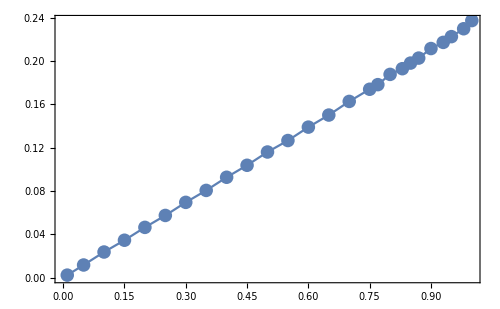

```mathematica
dataV=Sort[{#1,dBmToVolts[#2]}&@@@responseData];
ListLinePlot[dataV,Mesh->All]
```

```mathematica
lmf=LinearModelFit[dataV,x,x]
```

FittedModel[-0.00103276+0.234799 x]

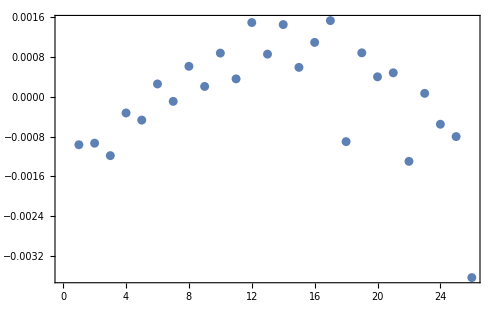

```mathematica
ListPlot[(lmf[#1]-#2)&@@@lmf["Data"]]
```

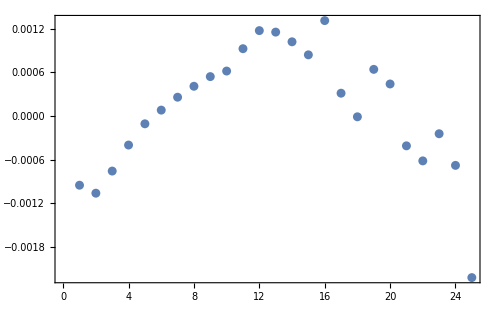

```mathematica
ListPlot[MovingAverage[(lmf[#1]-#2)&@@@lmf["Data"],2]]
```

```mathematica
dataVinterp=Interpolation[dataV~Join~(-1*dataV)]
```

InterpolatingFunction[…]

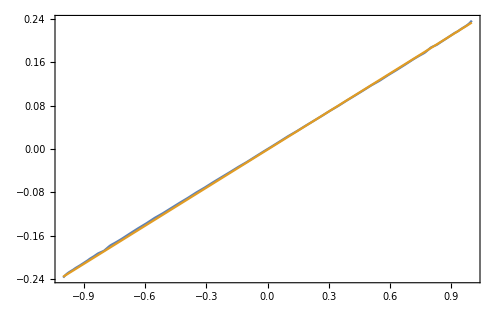

```mathematica
Plot[{dataVinterp[x],lmf[x]},{x,-1,1}]
```

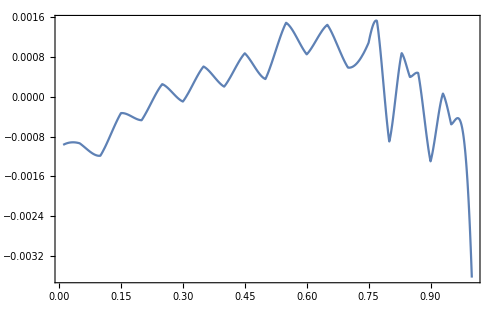

```mathematica
Plot[{lmf[x]-dataVinterp[x]},{x,0.01,1}]
```

```mathematica
sol=x/.Solve[dataVinterp[x]==y,x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

InverseFunction[InterpolatingFunction[…],1,1][y]

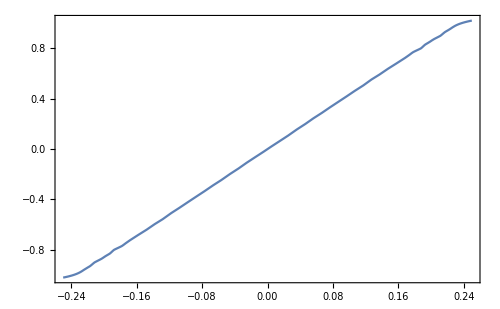

```mathematica
Plot[sol/.y->Y,{Y,-0.25,0.25}]
```

```mathematica
inverseF[x_?NumericQ]:=sol/.y->x//Evaluate
```

```mathematica
inverseF[-0.1]
```

-0.433156

```mathematica
Plot[inverseF[Y],{Y,-0.25,0.25}]
```

-Graphics-

```mathematica
dt=1000/800.
```

1.25

```mathematica
targetPulseData=Table[(a*Sin[2π*(200+df)*10^6*t*dt*10^-9]-a*Sin[2π*(200-df)*10^6*t*dt*10^-9])/.{a->0.12,df->5},{t,1,160,dt}];
```

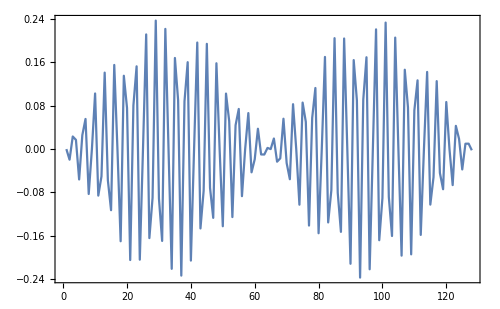

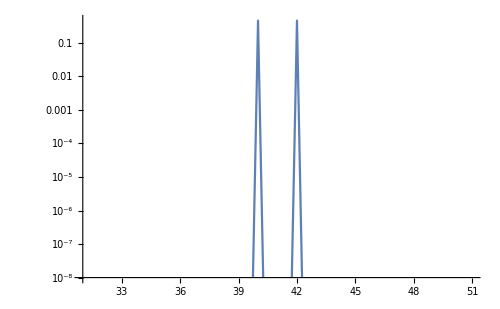

```mathematica
ListLinePlot[targetPulseData]
ListLogPlot[Abs[Fourier[targetPulseData]]^2,PlotRange->{{31,51},{10^-8,All}},Joined->True]
```

```mathematica
1
```

```mathematica
correctedPulseData=0.25*inverseF/@targetPulseData;
```

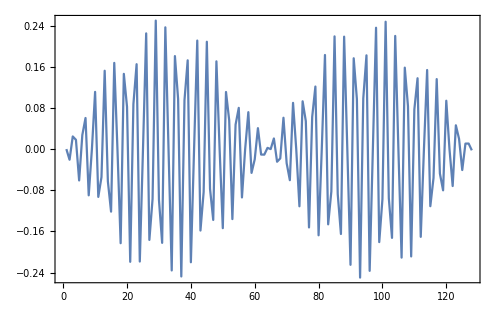

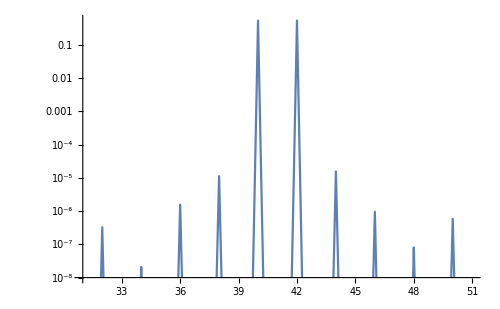

```mathematica
ListLinePlot[correctedPulseData]
ListLogPlot[Abs[Fourier[correctedPulseData]]^2,PlotRange->{{31,51},{10^-8,All}},Joined->True]
```

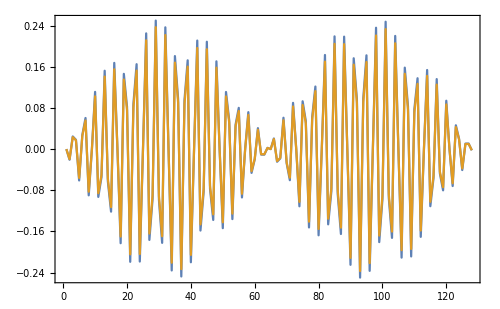

```mathematica
ListLinePlot[{correctedPulseData,targetPulseData}]
```

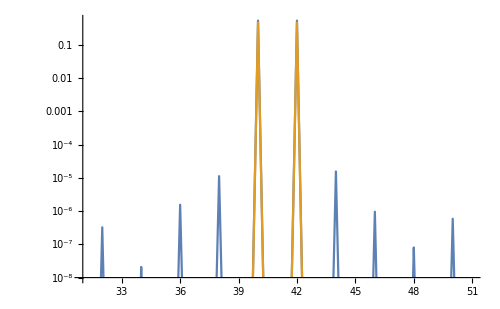

```mathematica
ListLogPlot[{MovingAverage[Abs[Fourier[Flatten[Table[correctedPulseData,#]]]]^2,1],MovingAverage[Abs[Fourier[Flatten[Table[targetPulseData,#]]]]^2,1]},PlotRange->{{31,51}*#,{10^-8,All}},Joined->True]&[1]
```

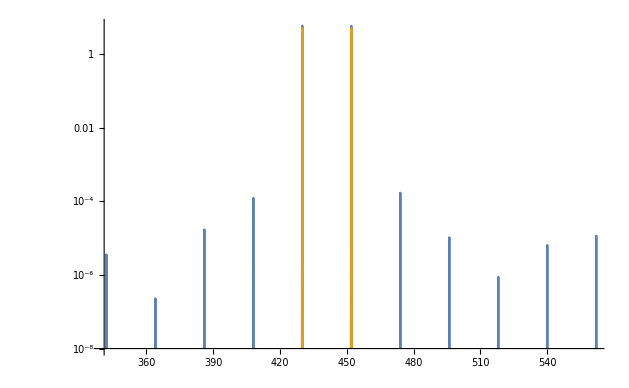

```mathematica
ListLogPlot[{Abs[Fourier[Flatten[Table[correctedPulseData,#]]]]^2,Abs[Fourier[Flatten[Table[targetPulseData,#]]]]^2},PlotRange->{{31,51}*#,{10^-8,All}},Joined->True]&[11]
```